## Inicialize some functions

```mathematica
Remove["Global`*"]
```

```mathematica
<<CompiledFunctionTools`;
Needs["NumericalCalculus`"]
<<MaTeX`
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
densityPlotOptionsExport={PerformanceGoal->"Quality",PlotRange->Full,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"}
exportOptions={"AllowRasterization"->True,ImageSize->340,ImageResolution->800};
```

{PerformanceGoal→Quality,PlotRange→Full,FrameLabel→{-Graphics-,-Graphics-},{BaseStyle→Directive[FontSize→12],AxesStyle→Directive[FontSize→12],TicksStyle→Directive[FontSize→12],LabelStyle→{FontFamily→Latin Modern Roman,FontSize→12},BaseStyle→texStyle},ColorFunction→SunsetColors}

## Defining the Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
as={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

# N = 3

```mathematica
nn=3;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m]
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}]
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

{{-3/2-λ/4,-χ/(2 √3),-λ/(2 √3),0},{-χ/(2 √3),-1/2+1/3 (-(7 λ)/4-χ^2),-χ,-λ/(2 √3)},{-λ/(2 √3),-χ,1/2+1/3 (-(7 λ)/4-4 χ^2),-(5 χ)/(2 √3)},{0,-λ/(2 √3),-(5 χ)/(2 √3),3/2+1/3 (-(3 λ)/4-9 χ^2)}}

```mathematica
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort,en,eig,eigNon,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig[[1]]].DH1C[λ,χ].eig[[#]]&/@Range[2,dim];
M1T=Conjugate[eig[[#]]].DH1C[λ,χ].eig[[1]]&/@Range[2,dim];
M2=Conjugate[eig[[1]]].DH2C[λ,χ].eig[[#]]&/@Range[2,dim];
M2T=Conjugate[eig[[#]]].DH2C[λ,χ].eig[[1]]&/@Range[2,dim];
endif=(en[[1]]-en[[#]])^2&/@Range[2,dim];
g11=Re@Sum[(M1[[i]]M1T[[i]])/endif[[i]],{i,1,dim-1}];
g12=Re@Sum[(M1[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
g22=Re@Sum[(M2[[i]]M2T[[i]])/endif[[i]],{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

## Geodesics

```mathematica
derPiece[λ_,χ_]=Piecewise[{{14,λ>1&&-0.4<χ<0.4}},Round[8+10/(0.8+(λ+1/2)^2+(Abs[χ]-√(3/5))^2)]];
derPieceC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@derPiece[λ,χ],Evaluate@compileOptions];
```

```mathematica
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPieceC[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
eq={
λ''[t]+G1[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0,
χ''[t]+G2[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0
};
```

### Initial value problem

```mathematica
cauchy[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
```

```mathematica
Timing@Quiet@NDSolve[Join[eq,cauchy[0,0,Cos[-0.6],Sin[-0.6]]],{λ,χ},{t,0,10},PrecisionGoal->4,AccuracyGoal->4]
```

{2.9406,{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}}

```mathematica
solMulti=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[i],Sin[i]]],{λ,χ},{t,0,1}],{i,0.2,0.6,0.1}]
```

{{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}}

```mathematica
solMulti1=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,0.1Cos[i],0.1Sin[i]]],{λ,χ},{t,0,10}],{i,0.2,0.6,0.1}]
```

{{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}}

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-1.5,2},{χ,-1,1},Evaluate@densityPlotOptionsExport,ScalingFunctions->"Log10",PlotPoints->100];
```

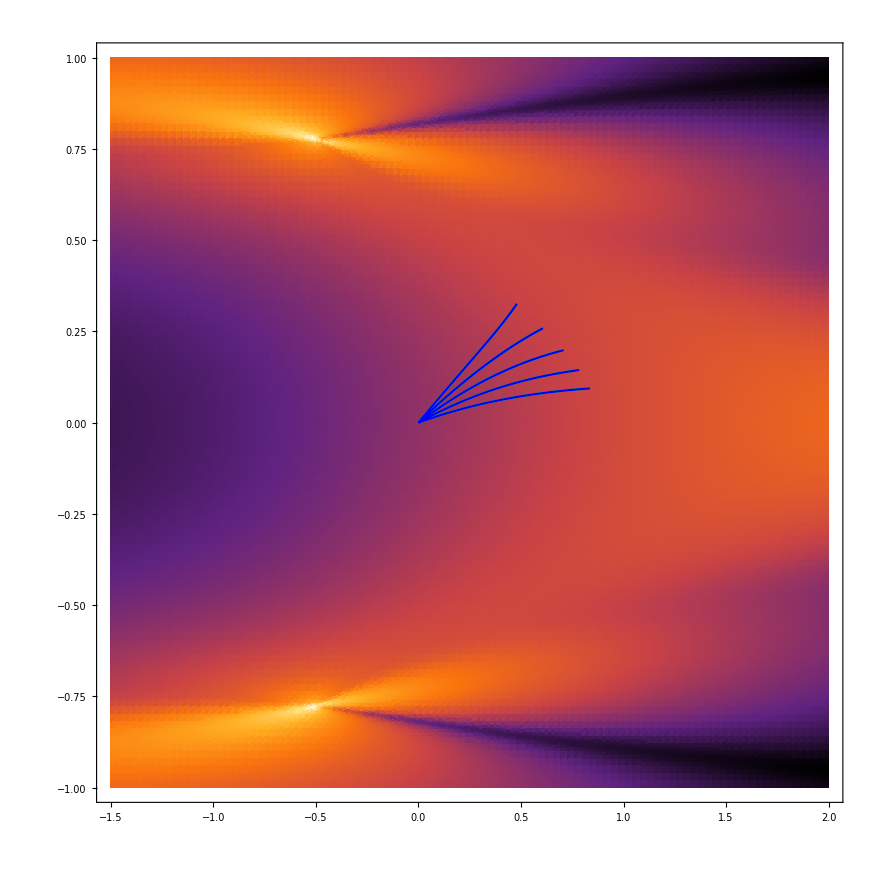

```mathematica
geodBoundary=ParametricPlot[{λ[t],χ[t]}/.solMulti,{t,0,1},PlotRange->All,Frame->True,PlotStyle->Green];
geodBoundary1=ParametricPlot[{λ[t],χ[t]}/.solMulti1,{t,0,10},PlotRange->All,Frame->True,PlotStyle->Blue];
Show[{geodbg,geodBoundary,geodBoundary1}]
```

```mathematica
Flatten[{λ[1],χ[1]}/.solMulti]-Flatten[{λ[10],χ[10]}/.solMulti1]
```

{7.15217×10^-8,1.9694×10^-8,7.02885×10^-8,2.24021×10^-8,2.52195×10^-8,6.91945×10^-9,1.95339×10^-8,6.8619×10^-9,1.73804×10^-8,7.6523×10^-9}

```mathematica
solMultileft=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[i],Sin[i]]],{λ,χ},{t,0,1}],{i,π-0.225,π,0.01}];
```

```mathematica
Export[NotebookDirectory[]<>"solMulti_N=3_part1_mintheta=pi-0,205.m",solMultileft]
```

/home/strelda/Documents/mff/dp/code/metacentrum/solMulti_N=3_part1_mintheta=pi-0,207.m

```mathematica
solMultileft1=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[i],Sin[i]]],{λ,χ},{t,0,12}],{i,π-0.220,π-0.206,0.001}]
```

{{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}}

```mathematica
Export["/home/strelda/Documents/mff/dp/code/savedData/solMulti_N=3_part2_mintheta=pi-0,220.m",solMultileft1]
```

/home/strelda/Documents/mff/dp/code/savedData/solMulti_N=3_part2_mintheta=pi-0,220.m

```mathematica
solMultileft2=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[i],Sin[i]]],{λ,χ},{t,0,15}],{i,π-0.225,π-0.221,0.001}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.0659×10^-11,-4.94523×10^-8},{-4.94523×10^-8,0.000230542}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.06553×10^-11,-4.94407×10^-8},{-4.94407×10^-8,0.000230513}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{{{λ→InterpolatingFunction[{{0., 15.}}, <>],χ→InterpolatingFunction[{{0., 15.}}, <>]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}}

```mathematica
Export["/home/strelda/Documents/mff/dp/code/savedData/solMulti_N=3_part3_mintheta=pi-0,225.m",solMultileft2]
```

/home/strelda/Documents/mff/dp/code/savedData/solMulti_N=3_part2_mintheta=pi-0,225.m

```mathematica
solMultileft3=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[i],Sin[i]]],{λ,χ},{t,0,15}],{i,π-0.229,π-0.226,0.001}]
```

NDSolve::ndsz: At t == 6.86448, step size is effectively zero; singularity or stiff system suspected.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.37793×10^-11,-6.09188×10^-8},{-6.09188×10^-8,0.000270503}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.48364×10^-11,-6.42871×10^-8},{-6.42871×10^-8,0.000279733}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.483×10^-11,-6.42686×10^-8},{-6.42686×10^-8,0.000279692}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.7732×10^-12,-4.07633×10^-8},{-4.07633×10^-8,0.000190318}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{8.77231×10^-12,-4.07606×10^-8},{-4.07606×10^-8,0.000190312}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 784060 steps reached at the point t == 14.5958.

NDSolve::mxst: Maximum number of 783804 steps reached at the point t == 14.8793.

NDSolve::mxst: Maximum number of 784317 steps reached at the point t == 14.1723.

{{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[{{0., 14.1723}}, <>],χ→InterpolatingFunction[{{0., 14.1723}}, <>]}},{{λ→InterpolatingFunction[{{0., 14.5958}}, <>],χ→InterpolatingFunction[{{0., 14.5958}}, <>]}},{{λ→InterpolatingFunction[{{0., 14.8793}}, <>],χ→InterpolatingFunction[{{0., 14.8793}}, <>]}}}

```mathematica
Export["/home/strelda/Documents/mff/dp/code/savedData/solMulti_N=3_part4_mintheta=pi-0,229.m",solMultileft3]
```

/home/strelda/Documents/mff/dp/code/savedData/solMulti_N=3_part4_mintheta=pi-0,229.m

```mathematica
solMultibottom=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[-1,i,1,0]],{λ,χ},{t,0,5},AccuracyGoal->3,PrecisionGoal->3],{i,-3,3,0.1}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.9544×10^-12,1.15863×10^-8},{1.15863×10^-8,0.0000691957}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.92982×10^-12,1.14789×10^-8},{1.14789×10^-8,0.0000687829}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.27013×10^-11,5.70865×10^-8},{5.70865×10^-8,0.000257637}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.25189×10^-11,5.65111×10^-8},{5.65111×10^-8,0.000256144}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

NDSolve::ndcf: Repeated convergence test failure at t == 1.69009; unable to continue.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.97241×10^-12,-1.16569×10^-8},{-1.16569×10^-8,0.0000694036}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.94897×10^-12,-1.15548×10^-8},{-1.15548×10^-8,0.0000690131}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.26832×10^-11,-5.7027×10^-8},{-5.7027×10^-8,0.000257466}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.25028×10^-11,-5.64576×10^-8},{-5.64576×10^-8,0.000255988}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

NDSolve::mxst: Maximum number of 10000 steps reached at the point t == 1.66432.

NDSolve::ndcf: Repeated convergence test failure at t == 3.16986; unable to continue.

```mathematica
Export["solMulti_N=3_lambdaIn=-1.m",solMultibottom]
```

solMulti_N=3_lambdaIn=-1.m

```mathematica
solMulti1=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[i],Sin[i]]],{λ,χ},{t,0,10}],{i,-0.63,0,0.01}];
```

```mathematica
Export[NotebookDirectory[]<>"solMulti_N=3_maxtheta=-0,63.m",solMulti1]
```